```mathematica
Button["Начать сначала", Remove["Global`*"]; FrontEndTokenExecute@"EvaluateInitialization";]
```

Начать сначала

```mathematica
parentPath=$InputFileName/."":>NotebookFileName[];
parentDir=DirectoryName@parentPath;
SetDirectory[parentDir]
Print[parentDir]
```

C:\Users\zhuko\Google Диск\Ирина\MathModelWeb\static

C:\Users\zhuko\Google Диск\Ирина\MathModelWeb\static\

```mathematica
"Значения констант по-умолчанию для сплава Ti-Al";
METR2CM:=100;
GRAMPERMOL:=36.38;

ks:=29.22/METR2CM;
kl:=29/METR2CM;
k:=0.8;

gl:=1;

L:=12268.8/GRAMPERMOL;
rho:=3.46;
LV:=L*rho;

Dl:=8.27*10^(-9)*METR2CM*METR2CM;

T0:=0;
sigmaInf:=0.55;

m:=-8.8;

gsMin:=2;
gsMax:=25;

nmin :=-2;
nmax:=2;
```

```mathematica
getArg[args_, varName_, default_]:= If[KeyExistsQ[args, varName], Internal`StringToDouble[args[varName]], default];

args :=Association[Import["args.json"]];

ks= getArg[args,"ks", ks];
kl= getArg[args,"kl", kl];
k= getArg[args,"k", k];

gl= getArg[args,"gl", gl];

L = getArg[args,"L", L];
rho = getArg[args,"rho", rho];
LV=L*rho;

Dl = getArg[args,"Dl", Dl];
sigmaInf = getArg[args,"sigmaInf", sigmaInf];
m = getArg[args,"m", m];

gsMin = getArg[args,"gsMin", gsMin];
gsMax = getArg[args,"gsMax", gsMax];

nmin =getArg[args,"nmin", nmin];
nmax=getArg[args,"nmax", nmax];
```

```mathematica
Dl
```

0.0000827

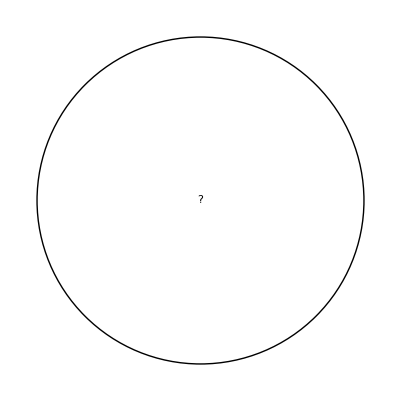
t |  |  K   | °C | 
e |  | кал   | Дж | 
k_s |  | 
k_l |  | 
k |  | 
g_l |  | 
L |  | 
ρ |  | г/см^3
L_V |  | 
D_l |  | см^2/сек
σ_∞ |  | 
m |  | -Graphics-  Введите значения констант:

Границы для  n

```mathematica
addRow[varName_, var_, tooltip_, units_]:={
Tooltip[varName, tooltip], InputField[var, Number], units
};

Panel[
Grid[{
{Tooltip["t","Единицы измерения температуры"],RadioButtonBar[Dynamic[temperature],{" K","°C"}],""},
{Tooltip["e","Единицы измерения энергии"],RadioButtonBar[Dynamic[energy],{"кал","Дж"}],""},
addRow[Subscript["k", "s"],Dynamic[ks], "Коэффициент теплопроводности по твёрдой фазе", Dynamic[StringJoin[energy,"/сек см",temperature]]],
addRow[Subscript["k", "l"], Dynamic[kl],"Коэффициент теплопроводности по жидкой фазе", Dynamic[StringJoin[energy,"/сек см",temperature]]],
addRow["k",Dynamic[k], "Равновесный коэффициент распределения примеси",""], 
addRow[Subscript["g", "l"],Dynamic[gl],"Градиент температуры в жидкой фазе",Dynamic[StringJoin[temperature,"/см"]]],
addRow["L", Dynamic[L], "Скрытая теплота затвердевания", Dynamic[StringJoin[energy,"/г"]]],
addRow[ρ, Dynamic[rho], "Плотность", "г/(:0441:043c)^3"],
{Tooltip[Subscript["L", "V"], "Скрытая теплота затвердевания"],Dynamic[LV],Dynamic[StringJoin[energy,"/(:0441:043c)^3"]]},
addRow[Subscript["D", "l"], Dynamic[Dl], "Коэффициент диффузии примеси по жидкой фазе", "(:0441:043c)^2/сек"],
addRow[Subscript[σ, ∞], Dynamic[sigmaInf], "Концентрация примеси в расплаве вдали от двухфазной зоны",""],
addRow["m", Dynamic[m], "Наклон линии ликвидуса", Dynamic[StringJoin[temperature,"/вт%"]]]
}],
Row[Pane[#,{Automatic,15}]&/@ {MouseAppearance[Tooltip[Graphics[{Circle[], Text["?"]}], "Наведите курсор на имя константы, чтобы узнать её смысл"], "LinkHand"],Text["  Введите значения констант:"]}]
]

Panel[Row[{"Границы для "Tooltip["n", "Коэффициент отклонения уравнения ликвидуса от линейного вида"],IntervalSlider[Dynamic[{nmin, nmax}],{-3,3,1},Appearance->{"ThumbAppearance"->{Dynamic[Framed[nmin,Background->White]],None,Dynamic[Framed[nmax,Background->White]]}}, Method->"Stop", MinIntervalSize -> 1 ],Dynamic[{nmin, nmax}]}],FrameMargins->15]
```

Графики отклонения уравнения ликвидуса от линейного вида:

```mathematica
Tm[sigmaM_, n_]:=T0+m*sigmaM+n*sigmaM^2;
```

```mathematica
Manipulate[
 Plot[{Tm[sigmaM, n]}, {sigmaM, 0, 1},
  AxesLabel -> {Subscript[σ, 𝓂], Subscript[T, 𝓂]}, 
  GridLines -> Automatic, 
  PlotLegends -> "𝓃=" <> ToString[n]
  ], 
 {{n, nmin, "Коэффициент отклонения уравнения ликвидуса:"}, nmin, nmax}]
```

```mathematica
Manipulate[
 Plot[Evaluate@Table[Tm[sigmaM, n], {n, chosenN}], {sigmaM, 0, 1},
  AxesLabel -> {Subscript[σ, 𝓂], Subscript[T, 𝓂]},
  PlotLegends -> LineLegend[Table[n, {n, chosenN}], LegendLabel -> 𝓃]],
 {
  {chosenN, {0}, "Коэффициент отклонения уравнения ликвидуса:"},
  Range[nmin, nmax],
  ControlType -> CheckboxBar
  }
 ]
```

Для пересчёта модели пересчитайте следующую клетку:

```mathematica
km[phi_]:=ks*phi + kl*(1-phi);
Diff[phi_]:=Dl*(1-phi);

us := (ks*gs - kl*gl)/LV;
D0[phi_]:= Diff[phi]/Dl;

Tm[sigmaM_]:=T0+m*sigmaM+n*sigmaM^2;
f [sigmaM_]:=D[Tm[sigmaMI], sigmaMI] /.sigmaMI->sigmaM;
f0:= f[0];

r:=(2*n*sigmaInf)/m;
L0[phi_]:=phi +kl/ks*(1-phi);
Ll := kl/ks;
P := (ks*f0*sigmaInf)/(LV*Dl);
Gl := (gl*Dl)/(us*f0*sigmaInf);

h[phi_] := (D0[phi]*(P*Ll*Gl + phi))/(P*L0[phi]);
b:=If[r≠0,(-(1+r)+√((1+r)^2-4*r*Gl))/(2*r), -Gl];

Eq1[phi_]:=((1-phi)*(1+r*Cm[phi])^2-r*h[phi])*Cm'[phi]+(k-1)*(1+r*Cm[phi])^2*Cm[phi]+(1+r*Cm[phi])*h'[phi];
sol1=ParametricNDSolve[{Eq1[phi]==0,Cm[0]==1+b},Cm,{phi,0,0.99},{n,gs}];
(*Считаем φ^**)
NCm[n_,gs_,phi_]:=Evaluate[Cm[n,gs][phi]/.sol1]

phistar=Table[phi/.FindRoot[(1-k)*NCm[n,gs,phi]*P*L0[phi]*(1+r/.n->n*NCm[n,gs,phi])+P*Ll*Gl+phi==0,{phi,0.8}],{n,nmin,nmax},{gs,gsMin,gsMax}];
phistarI[n_,gs_]:=ListInterpolation[phistar,InterpolationOrder->3,Method->"Spline"][n - nmin + 1,gs - gsMin + 1];

(*Считаем δ*)
g[n_, gs_,phi_] := 1+(r/.n->n)*NCm[n, gs, phi];
dNCmdx[n_, gs_, phi_] := (P*Ll*Gl+phi)/(P*L0[phi]*g[n, gs,phi]);
dxdphi[n_,gs_,phi_]:=  D[NCm[n,gs,phi],phi]/dNCmdx[n, gs, phi];
eps[n_,gs_]:=x[0]/. NDSolve[{dxdphi[n,gs,phi]-x'[phi]==0,x[phistarI[n,gs]]==0},x,{phi,0,0.01}];
```

InterpolatingFunction::dmval: Input value {-0.493418} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.18368} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-13.467} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
"Табличные значения φ"
(*ListPlot3D[phistar,AxesLabel->{Subscript[g, s],n,φ^*}, PlotRange->{0,1}]*)
```

Табличные значения φ

```mathematica
"Интерполирующая функция φ"
exportCSV[fileName_, data_]:=Export[fileName, TableForm[Join@@data], "CSV"];

phiIData = Table[phistarI[n,gs],{n,nmin,nmax}, {gs,gsMin,gsMax}];
exportCSV["phi_interpolated.csv", Table[{n, gs, phistarI[n,gs]},{n,nmin,nmax}, {gs,gsMin,gsMax}]];
```

Интерполирующая функция φ

```mathematica
(*phiIPlot =Plot3D[phistarI[n,gs],{n,nmin,nmax}, {gs,gsMin,gsMax},AxesLabel->{n,Subscript[g, s],φ^*}, PlotRange->{0,1}];
Export["phi_interpolated.png",phiIPlot];*)
```

```mathematica
Show[phiIPlot]
```

-Graphics3D-

Доля твёрдой фазы на границе кристалл-двухфазная зона в зависимости от градиента температуры в твёрдой фазе g_s и коэффициента отклонения уравнения ликвидуса от линейного вида 𝓃

```mathematica
Manipulate[Plot3D[phistarI[n,gs],{n,localNInterval[[1]], localNInterval[[2]]}, {gs,localgsInterval[[1]], localgsInterval[[2]]},AxesLabel->{n,Subscript[g, s],SuperStar[φ]}, PlotRange->{0,1}],
{{localNInterval,{nmin, nmax, 0.2},
Row[{"Коэффициент отклонения уравнения ликвидуса:"}]
},nmin,nmax,ControlType->IntervalSlider,Appearance->"Paired",Method->"Stop", MinIntervalSize -> 0.2
},
{{localgsInterval,{gsMin, gsMax},
Row[{"Градиент температуры в твёрдой фазе:"}]
},gsMin,gsMax,0.5,ControlType->IntervalSlider,Appearance->"Paired",Method->"Stop", MinIntervalSize -> 0.2
}
]
```

```mathematica
Manipulate[
Plot[{phistarI[n, gs]},{gs,gsMin,7},
AxesLabel->{Subscript[g, s],SuperStar[φ]}, 
GridLines->Automatic, 
PlotLegends->"n="<>ToString[n]
], 
{{n,nmin, "Коэффициент отклонения уравнения ликвидуса:"}, nmin, nmax}]
```

Plot::plln: Limiting value gsMin in {gs,gsMin,7} is not a machine-sized real number.

```mathematica
Manipulate[
Plot[Evaluate@Table[phistarI[n, gs],{n,chosenN}],{gs,gsMin,5},
AxesLabel->{Subscript[g, s],SuperStar[φ]},
PlotLegends->LineLegend[Table[n,{n, chosenN}],LegendLabel->n]],
{
{chosenN,{nmin, nmax}, "Коэффициент отклонения уравнения ликвидуса:"},
Range[nmin, nmax],
ControlType->CheckboxBar
}
]
```

Plot::plln: Limiting value gsMin in {gs,gsMin,5} is not a machine-sized real number.

```mathematica
Plot3D[NCm[n,gs, 0],{n,nmin,nmax}, {gs,gsMin,gsMax},AxesLabel->{n,Subscript[g, s],"C_m"}]
```

-Graphics3D-

Концентрация примеси в двухфазной зоне в зависимости от градиента температуры в твёрдой фазе g_s и коэффициента отклонения уравнения ликвидуса от линейного вида 𝓃

```mathematica
Manipulate[Plot3D[NCm[n,gs, 0],{n,localNInterval[[1]], localNInterval[[2]]}, {gs,localgsInterval[[1]], localgsInterval[[2]]},AxesLabel->{n,Subscript[g, s],"C_m"}],
{{localNInterval,{nmin, nmax},
Row[{"Коэффициент отклонения уравнения ликвидуса:"}]
},nmin,nmax,1,ControlType->IntervalSlider,Appearance->"Paired",Method->"Stop", MinIntervalSize ->0.5
},
{{localgsInterval,{gsMin,gsMax},
Row[{"Градиент температуры в твёрдой фазе:"}]
},gsMin,gsMax,1,ControlType->IntervalSlider,Appearance->"Paired",Method->"Stop", MinIntervalSize ->0.5
}
]
```

```mathematica
"Строим "ε
Plot3D[eps[n,gs],{n,nmin, nmax},{gs,gsMin,gsMax},AxesLabel->{n,Subscript[g, s],ε}]
```

Строим  ε

-Graphics3D-

```mathematica
Manipulate[Plot3D[eps[n,gs],{n,localNmin, localNmax}, {gs,localgsmin, localgsmax},AxesLabel->{n,Subscript[g, s],ε}],
Row[{Control[{{localNmin, nmin,"n_min"},Range[nmin, localNmax-1, 0.5], ControlType -> PopupMenu}],Spacer[50],
Control[{{localNmax, nmax,"n_max"},Range[localNmin+1, nmax, 0.5], ControlType -> PopupMenu}]}],
Row[{Control[{{localgsmin, gsMin,"g_s_min"},Range[gsMin, localgsmax-1, 0.5], ControlType -> PopupMenu}],Spacer[50],
Control[{{localgsmax, gsMax,"g_s_max"},Range[localgsmin+1, gsMax, 0.5], ControlType -> PopupMenu}]}]
]
```

```mathematica
"Строим δ[n, g]"
deltaPlot = Plot3D[Dl/us*eps[n,gs],{n,nmin,nmax},{gs,gsMin,gsMax},AxesLabel->{n,Subscript[g, s], δ}];
Show[deltaPlot]
":041f:0440:043e:0442:044f:0436:0435:043d:043d:043e:0441:0442:044c :043e:0431:043b:0430:0441:0442:0438 :0444:0430:0437:043e:0432:043e:0433:043e :043f:0435:0440:0435:0445:043e:0434:0430 :0432 :0437:0430:0432:0438:0441:0438:043c:043e:0441:0442:0438 :043e:0442 :0433:0440:0430:0434:0438:0435:043d:0442:0430 :0442:0435:043c:043f:0435:0440:0430:0442:0443:0440:044b :0432 :0442:0432:0435:0440:0434:043e:0439 :0444:0430:0437:0435 :043f:0440:0438 g "<>StringJoin[ToString[gl]," " ,temperature, "/:0441:043c"]
```

Строим δ[n, g]

-Graphics3D-

Протяженность области фазового перехода в зависимости от градиента температуры в твердой фазе при g 1  K/см

```mathematica
exportCSV["epsilon.csv", Table[{n, gs, eps[n,gs][[1]]},{n,nmin,nmax}, {gs,gsMin,gsMax}]];
exportCSV["delta.csv", Table[{n, gs, Dl/us*eps[n,gs][[1]]},{n,nmin,nmax}, {gs,gsMin,gsMax}]];
```